Horava 234B.2015
Course Prelimaries
 • Classical Gravity(GR)
 	geometric, gauge theory, relativistic, invariant under local spacetime symmetry
 	compatible w/Lagrangian-Hamiltonian formalism(path integral)
 	EM from variational principles (Exception of Type IIB supergravity which does not have S→∫ℒ
 • Use QFT logic
 • Arena: spacetime M←differential manifold {x^μ,{μ,0,D}}; spacetime dimension → d → D[spatial dimensions]+1
 	sometimes use Euclidean manifold M→ℝ^d
 • Fields: metric: g_μν[x^σ] → symmetric non-degenerate(g≠0) 2-tensor; g→Det[g_μν]
 	? non-degenerate g ⇒ background; does QG ⇒ no background?
 • Symmetries: Diff[M]→
 Mathematica does not display some compound symbols

```mathematica
<<Local`QFTToolKit`
Put[SaveFile=NBname["stub"]<>".out"]
```

```mathematica
PR["• Symmetries: ", Diff[M]->{x̃[x^σ],Det[xPartialD[x̃[x^σ],x^σ]]≠0},
Yield,T[g̃,"dd"][μ,ν][x̃]->xPartialD[x^σ,(x̃)^μ]xPartialD[x^ρ,(x̃)^ν]T[g,"dd"][σ,ρ][x],
NL,"Infinetessimal transform: Lie Algebra: ",(x̃)^μ->x^μ+(ξ^μ)[x],
Yield,T[g,"dd"][μ,ν]->T[g,"dd"][μ,ν]+δ[T[g,"dd"][μ,ν]],
Yield,δ[T[g,"dd"][μ,ν]]->T[ξ,"u"][σ] xPartialD[T[g,"dd"][μ,ν],σ]+T[g,"dd"][μ,λ] xPartialD[T[ξ,"u"][λ],ν]+T[g,"dd"][ν,λ] xPartialD[T[ξ,"u"][λ],μ],
yield,xCovariantD[T[ξ,"d"][ν],μ]+xCovariantD[T[ξ,"d"][μ],ν],
NL,"Work on tensors: ",
xCovariantD[T[t,"dduu"][μ,…,σ,…],λ]->xPartialD[T[t,"dduu"][μ,…,σ,…],λ]-T[Γ,"udd"][ρ,λ,μ]T[t,"dduu"][ρ,…,σ,…]+T[Γ,"udd"][σ,λ,ρ]T[t,"dduu"][ρ,…,μ,…],
NL,"• Field strengths: Riemann tensor: ",
T[R,"uddd"][μ,ν,σ,ρ]->xPartialD[T[Γ,"udd"][μ,ν,ρ],σ]-xPartialD[T[Γ,"udd"][μ,ν,σ],ρ]+T[Γ,"udd"][μ,σ,λ]T[Γ,"udd"][λ,ρ,ν]-T[Γ,"udd"][μ,ρ,λ]T[Γ,"udd"][λ,σ,ν],
NL,"Independent degrees of freedom: ",
{{dim[4]->6,T[R,"uddd"][μ,ν,σ,ρ]},
{dim[3]->2,T[R,"dd"][μ,ν]},
{dim[2]->1,R}
}//Column,
NL,"Ricci tensor: ",T[R,"dd"][ν,ρ]->T[R,"uddd"][μ,ν,μ,ρ],
yield," tensor ",imply,R[x]->0,imply,R[x']->0,
NL,"Ricci scalar: ",R->T[g,"uu"][μ,ν]T[R,"dd"][μ,ν],
NL,"• Typical decompositon: ",ℝ^d->ℝ^(d-n)⊗T^n,
NL,"• In experiments see only small deviation from flat.",
NL,"• Action: ",Subscript[S, EH]->1/(16π Subscript[G, n])IntegralOp[{{x^d}},√-g(R-2 Subscript[Λ, cosmological]+α R^2+β R.R+O[…])],
NL,"Other terms can exist: ",{α,β,…},
NL,"• Use organizing principles: RG[compare scale μ_rg to experiment], dimensional analysis,"
]
```

• Symmetries: Diff[M]→{x̃[x^σ],Det[UnderBar[∂]_(x^σ)[x̃[x^σ]]]≠0}
→ T[g̃,dd][μ,ν][x̃]→UnderBar[∂]_((x̃)^ν)[x^ρ] UnderBar[∂]_((x̃)^μ)[x^σ] T[g,dd][σ,ρ][x]
Infinetessimal transform: Lie Algebra: (x̃)^μ→x^μ+ξ^μ[x]
→ T[g,dd][μ,ν]→δ[T[g,dd][μ,ν]]+T[g,dd][μ,ν]
→ δ[T[g,dd][μ,ν]]→UnderBar[∂]_ν[T[ξ,u][λ]] T[g,dd][μ,λ]+UnderBar[∂]_μ[T[ξ,u][λ]] T[g,dd][ν,λ]+UnderBar[∂]_σ[T[g,dd][μ,ν]] T[ξ,u][σ] ⟶ (𝔇̲)_ν[T[ξ,d][μ]]+(𝔇̲)_μ[T[ξ,d][ν]]
Work on tensors: (𝔇̲)_λ[T[t,dduu][μ,…,σ,…]]→UnderBar[∂]_λ[T[t,dduu][μ,…,σ,…]]-T[t,dduu][ρ,…,σ,…] T[Γ,udd][ρ,λ,μ]+T[t,dduu][ρ,…,μ,…] T[Γ,udd][σ,λ,ρ]
• Field strengths: Riemann tensor: T[R,uddd][μ,ν,σ,ρ]→UnderBar[∂]_σ[T[Γ,udd][μ,ν,ρ]]-UnderBar[∂]_ρ[T[Γ,udd][μ,ν,σ]]-T[Γ,udd][λ,σ,ν] T[Γ,udd][μ,ρ,λ]+T[Γ,udd][λ,ρ,ν] T[Γ,udd][μ,σ,λ]
Independent degrees of freedom: {dim[4]→6,T[R,uddd][μ,ν,σ,ρ]}
{dim[3]→2,T[R,dd][μ,ν]}
{dim[2]→1,R}
Ricci tensor: T[R,dd][ν,ρ]→T[R,uddd][μ,ν,μ,ρ] ⟶  tensor  ⇒ R[x]→0 ⇒ R[x']→0
Ricci scalar: R→T[g,uu][μ,ν] T[R,dd][μ,ν]
• Typical decompositon: ℝ^d→ℝ^(d-n)⊗T^n
• In experiments see only small deviation from flat.
• Action: S_EH→(∫_{x^d} [√-g (R+R^2 α+β R.R-2 Λ_cosmological)+O[…]^1])/(16 π G_n)
Other terms can exist: {α,β,…}
• Use organizing principles: RG[compare scale μ_rg to experiment], dimensional analysis,

2015.1.27

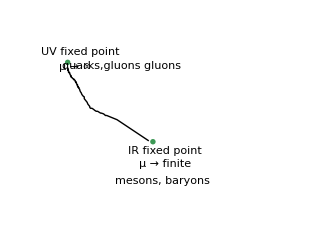
```mathematica
PR["Classical Gravity on manifold: ",M[dim[d]->"D"[spatial]+1],
NL,"use Metric: ",$g=T[g,"dd"][μ,ν][x],
NL,"use variational principle: ",Subscript[S, EH]->1/(16π Subscript[G, n])IntegralOp[{{x^d}},√-g(R-2 Subscript[Λ, cosmological]+α R^2+β R.R+O[…])],
NL,"Can define: ",𝒵->1/Vol[GaugeGroup[$g]] IntegralOp[{{$g}},Exp[I S]],
NL,"Does this make sense? Is it UV-complete?",
NL,"Use RG: compare μ_rg with intrinsic scales.",
NL,"• UV-complete scenarios: QCD->self-consistent. The picture is:",-Graphics-,
NL,CR["Reference: Wikipedia: Assymptotic safety"]
];
```

Classical Gravity on manifold: M[dim[d]→1+D[spatial]]
use Metric: g_μν^μν[x]
use variational principle: S_EH→(∫_{x^d} [√-g (R+R^2 α+β R.R-2 Λ_cosmological)+O[…]^1])/(16 π G_n)
Can define: 𝒵→(∫_{g_μν^μν[x]} [ⅇ^(ⅈ S)])/Vol[GaugeGroup[g_μν^μν[x]]]
Does this make sense? Is it UV-complete?
Use RG: compare μ_rg with intrinsic scales.
• UV-complete scenarios: QCD->self-consistent. The picture is:-Graphics-
Reference: Wikipedia: Assymptotic safety

```mathematica
PR["UV-incomplete example is fermion interaction: ",
S->IntegralOp[{{}},ψ.PartialDSlash[ψ]-m
ψ.ψ-Subscript[G, f](ψ.ψ)^2],
NL,"This action generates infinite number of terms: ", α Subscript[G, f]+β Subscript[G, f]^2+O[…] ," which often solved by an effective field theory ⇒ new particles, exotic states. ",
NL,"• Can use dimensional analysis in vicinity of a free theory to investigate Gaussian fixed points.",
NL,"• EX.1. Scalar field: ",S->1/2 IntegralOp[{{x^d}},xPartialD[ϕ,μ]xPartialDu[ϕ,μ]],
Yield,$=HoldForm[dim[S]->-d+1+dim[ϕ]+1+dim[ϕ]],
yield,$=(ReleaseHold[$]//Last)->0,
yield,$dϕ=tuRuleSolve[$,dim[ϕ]][[1]];Framed[$dϕ],
NL,"Implies connection with QG and Strings.",
NL,"• For interacting fields: ",
S->1/2 IntegralOp[{{x^d}},xPartialD[ϕ,μ]xPartialDu[ϕ,μ]-m^2 ϕ.ϕ-λ (ϕ.ϕ)^2],
Yield,$=HoldForm[dim[S]->-d+dim[λ]+4 dim[ϕ]],
yield,$=(ReleaseHold[$]//Last)->0,
yield,$dλ=tuRuleSolve[$,dim[λ]][[1]],
yield,$dλ=$dλ/.$dϕ//Simplify;Framed[$dλ]
];
```

UV-incomplete example is fermion interaction: S→∫_{} [-m ψ.ψ+ψ.(/∂ψ)-(ψ.ψ)^2 G_f]
This action generates infinite number of terms: (α G_f+β G_f^2)+O[…]^1 which often solved by an effective field theory ⇒ new particles, exotic states. 
• Can use dimensional analysis in vicinity of a free theory to investigate Gaussian fixed points.
• EX.1. Scalar field: S→1/2 ∫_{x^d} [UnderBar[∂]_μ[ϕ] UnderBar[∂]^μ[ϕ]]
→ dim[S]→-d+1+dim[ϕ]+1+dim[ϕ] ⟶ 2-d+2 dim[ϕ]→0 ⟶ dim[ϕ]→1/2 (-2+d)
Implies connection with QG and Strings.
• For interacting fields: S→1/2 ∫_{x^d} [-m^2 ϕ.ϕ-λ (ϕ.ϕ)^2+UnderBar[∂]_μ[ϕ] UnderBar[∂]^μ[ϕ]]
→ dim[S]→-d+dim[λ]+4 dim[ϕ] ⟶ -d+dim[λ]+4 dim[ϕ]→0 ⟶ dim[λ]→d-4 dim[ϕ] ⟶ dim[λ]→4-d

```mathematica
PR["● Definition: coupling categories: ",
NL,
{{"relevant"->dim[λ]>0},
{"marginal"->dim[λ]==0,"EG:d→1+1",xPartialD[ϕ^I,μ]xPartialDu[ϕ^J,μ]Subscript[G, IJ][ϕ,g[field]]},
{"irrelevant"->dim[λ]<0}}//Column,
NL,"(Ir)relevance defined in asymptotic safety."
]
```

● Definition: coupling categories: 
{relevant→dim[λ]>0}
{marginal→dim[λ]==0,EG:d→1+1,UnderBar[∂]_μ[ϕ^ⅈ] UnderBar[∂]^μ[ϕ^J] G_IJ[ϕ,g[field]]}
{irrelevant→dim[λ]<0}
(Ir)relevance defined in asymptotic safety.

```mathematica
PR["• EX.2. QED/YM: ",{S->-1/(4 Subscript[g, YM]^2)IntegralOp[{{x^4}},F.F],T[F,"dd"][μ,ν]->xPartialD[T[A,"d"][ν],μ]-xPartialD[T[A,"d"][μ],ν],dim[F]->2,dim[Subscript[g, YM]]->(4-d)/2},
NL,"A is geometric: ",xPartialD[_,μ],yield,xCovariantD[_,μ]->xPartialD[_,μ]+I T[A,"d"][μ],
NL,"In case of QCD g is marginally relavant: ",HoldForm[Limit[g,μ->∞]->0],
NL,"In case of QED g is marginally irrelevant ⇒ new particles."
]
```

• EX.2. QED/YM: {S→-(∫_{x^4} [F.F])/(4 g_YM^2),F_μν^μν→-UnderBar[∂]_ν[A_μ^μ]+UnderBar[∂]_μ[A_ν^ν],dim[F]→2,dim[g_YM]→(4-d)/2}
A is geometric: UnderBar[∂]_μ[_] ⟶ (𝔇̲)_μ[_]→ⅈ A_μ^μ+UnderBar[∂]_μ[_]
In case of QCD g is marginally relavant: Limit[g,μ→∞]→0
In case of QED g is marginally irrelevant ⇒ new particles.

```mathematica
PR["• EX.3. Fermions: ",{S->IntegralOp[{{x^d}},ψ̄.PartialDSlash[ψ]-m
ψ̄.ψ-Subscript[G, f](ψ̄.ψ)^2]},
Yield,$=HoldForm[dim[S]->-d+1+dim[ψ̄]+dim[ψ]],
NL,"Assume: ",$s=dim[ψ̄]->dim[ψ],
Yield,$=(ReleaseHold[$]/.$s//Last)->0,
yield,$dψ=tuRuleSolve[$,dim[ψ]][[1]];Framed[$dψ],
NL,"For ",dim[Subscript[G, f]],
Yield,$=HoldForm[dim[S]->-d+dim[Subscript[G, f]]+2 dim[ψ̄]+2 dim[ψ]],
Yield,$=(ReleaseHold[$]/.$s/.$dψ//Last)->0,
yield,$dg=tuRuleSolve[$,dim[Subscript[G, f]]][[1]];Framed[$dg],
NL,"Then scattering amplitudes ∼ ",Subscript[G, f]+Subscript[G, f]^2"E"^2+O[…],
imply,"UV-incomplete"


]
```

• EX.3. Fermions: {S→∫_{x^d} [-m ψ̄.ψ+ψ̄.(/∂ψ)-(ψ̄.ψ)^2 G_f]}
→ dim[S]→-d+1+dim[ψ̄]+dim[ψ]
Assume: dim[ψ̄]→dim[ψ]
→ 1-d+2 dim[ψ]→0 ⟶ dim[ψ]→1/2 (-1+d)
For dim[G_f]
→ dim[S]→-d+dim[G_f]+2 dim[ψ̄]+2 dim[ψ]
→ 2 (-1+d)-d+dim[G_f]→0 ⟶ dim[G_f]→2-d
Then scattering amplitudes ∼ (G_f+E^2 G_f^2)+O[…]^1 ⇒ UV-incomplete

```mathematica
PR["•Gravity: dimensions: ",
{d[s]^2->T[g,"uu"][μ,ν]d[T[x,"u"][μ]]d[T[x,"u"][ν]],dim[s]->-1,dim[T[x,"u"][ν]]->-1,dim[T[g,"uu"][μ,ν]]->0},
Imply,{dim[T[Γ,"udd"][μ,ν,λ]]->1,dim[R]->2},
NL,"From: ",Subscript[S, EH]->1/(16π Subscript[G, n])IntegralOp[{{x^d}},√-g(R-2 Subscript[Λ, cosmological]+α R^2+β R.R+O[…])],
Yield,{dim[Subscript[Λ, cosmological]]->2,dim[Subscript[G, n]]->2-d},
Imply,"Critical dimension: ",Subscript[G, n]->d->1+1," Possibly related to Strings."
]
```

•Gravity: dimensions: {d[s]^2→d[x_μ^μ] d[x_ν^ν] g_μν^μν,dim[s]→-1,dim[x_ν^ν]→-1,dim[g_μν^μν]→0}
⇒ {dim[Γ_μνλ^μνλ]→1,dim[R]→2}
From: S_EH→(∫_{x^d} [√-g (R+R^2 α+β R.R-2 Λ_cosmological)+O[…]^1])/(16 π G_n)
→ {dim[Λ_cosmological]→2,dim[G_n]→2-d}
⇒ Critical dimension: G_n→d→2 Possibly related to Strings.

2015.1.29 Classical Gravity cont’d

```mathematica
PR["Since ",dim[g]->0,and,Subscript[S, EH]->1/(16π Subscript[G, n])IntegralOp[{{x^d}},√-g(R-2 Subscript[Λ, cosmological]+α R^2+β R.R+O[…])],CO["associate Λ with geometry"],
Yield,$=dim[Subscript[G, n]]->2-d," for ",$s=d->4,imply,$/.$s,
NL,"Defined: ",Subscript[l, p]->√(ℏ Subscript[G, n]/c^3)->HoldForm[10^-33]⇒{Subscript[Λ, c][large]/Subscript[G, n]->Subscript[ρ, vac]},
NL,"Observations: ",yield,{Subscript[ρ, vac]≠0[small]," l_p<<reality <<l_H"},
NL,"• Hierarchy problem: t'Hooft: 'Macroscopic law should follow from microscopic ones.'",
NL,"QFT, local renormalization has no feedback to UV assumption.  But gravity is possibly non-local: there is a connection between UV-IR.",
NL,CG["Ref: Applequest-Carazzono decoupling theorem ⇒ UV controls IR behavior. (Examine failure modes)."],
NL,"● Perturbative quantization of S_EH.",
NL,"• Need to define vacuum state: ",{Ket[0],static,"lowest energy","E".Ket[0]->0,"E".Ket[ϕ]>0},
NL,"• Turn on interactions.",
NL,"• Λ->0 case: EOM: ",T[R,"dd"][μ,ν]-1/2 R T[g,"dd"][μ,ν]+Λ T[g,"dd"][μ,ν]->8π Subscript[G, n] T[T,"dd"][μ,ν],
NL,"where ",{T[T,"dd"][μ,ν]->-2/(√-g)xD[δ][Subscript[S, matter],T[g,"uu"][μ,ν]],S->Subscript[S, EH]+Subscript[S, matter][xPartialD[_,_]->xCovariantD[_,_]]},
NL,"• 1st problem: ",Exists["unique candidate vacuum geometer",ForAll[Λ]],
NL,"Choose Minkowski spacetime: ",ℝ^d->ℝ^{D,1}," maximally symmetric.",
NL,"💡 Positive energy theorem in GR 1979-81 Witten(using spinors)",
NL,"💡 Defn: Energy is not local concept, ADM energy E_ADM via Hamiltonian." ,
NL,"💡 E_ADM of non-singular asymptotic flat spacetime obeying Einstein equations having dominate energy condition is ≥ 0",
NL,"💡 Minkowski spacetime is the only spacetime w/E_ADM==0.",
NL,"💡 With only sensible ",T[T,"dd"][μ,ν],
NL,"- weak energy condition: ",T[T,"dd"][μ,ν]T[t,"u"][μ]T[t,"u"][ν]≥0,∀t ->"time-like, eg: ",{ρ≥0,ρ+p≥0},
NL,"- dominant energy condition: ",T[T,"dd"][μ,ν]T[t,"u"][μ]," space-like, eg: ",ρ≥Abs[p],
NL,"EX: Schwarzschild solution: M>0 ⇒ E_ADM→M, but M<0 ⇒ E_ADM<0 inconsistent with theorem.",
NL,"• Theorem ⇒ ∞ of spacetimes ↔ asymptotically flat is meaningless unless conformal(Weyl) compactification used (Penrose diagrams): ",
{T[g,"dd"][μ,ν]->T[g,"dd"][μ,ν] Ω[x]^2,{Ω[x],smooth},"preserves lightcone-causal structure"},
]
```

Since dim[g]→0 and S_EH→(∫_{x^d} [√-g (R+R^2 α+β R.R-2 Λ_cosmological)+O[…]^1])/(16 π G_n)associate Λ with geometry
→ dim[G_n]→2-d for d→4 ⇒ dim[G_n]→-2
Defined: l_p→√((ℏ G_n)/c^3)→1/10^33⇒{Λ_c[large]/G_n→ρ_vac}
Observations:  ⟶ {ρ_vac≠0[small], l_p<<reality <<l_H}
• Hierarchy problem: t'Hooft: 'Macroscopic law should follow from microscopic ones.'
QFT, local renormalization has no feedback to UV assumption.  But gravity is possibly non-local: there is a connection between UV-IR.
Ref: Applequest-Carazzono decoupling theorem ⇒ UV controls IR behavior. (Examine failure modes).
● Perturbative quantization of S_EH.
• Need to define vacuum state: {|0⟩,static,lowest energy,E.|0⟩→0,E.|ϕ⟩>0}
• Turn on interactions.
• Λ->0 case: EOM: -1/2 R g_μν^μν+Λ g_μν^μν+R_μν^μν→8 π G_n T_μν^μν
where {T_μν^μν→-(2 (δ̲)_(g_μν^μν)[S_matter])/(√-g),S→S_EH+S_matter[UnderBar[∂]__[_]→(𝔇̲)__[_]]}
• 1st problem: ∃_(unique candidate vacuum geometer)ForAll[Λ]
Choose Minkowski spacetime: ℝ^d→{ℝ^D,ℝ} maximally symmetric.
💡 Positive energy theorem in GR 1979-81 Witten(using spinors)
💡 Defn: Energy is not local concept, ADM energy E_ADM via Hamiltonian.
💡 E_ADM of non-singular asymptotic flat spacetime obeying Einstein equations having dominate energy condition is ≥ 0
💡 Minkowski spacetime is the only spacetime w/E_ADM==0.
💡 With only sensible T_μν^μν
- weak energy condition: t_μ^μ t_ν^ν T_μν^μν≥0ForAll[t]→time-like, eg: {ρ≥0,p+ρ≥0}
- dominant energy condition: t_μ^μ T_μν^μν space-like, eg: ρ≥Abs[p]
EX: Schwarzschild solution: M>0 ⇒ E_ADM→M, but M<0 ⇒ E_ADM<0 inconsistent with theorem.
• Theorem ⇒ ∞ of spacetimes ↔ asymptotically flat is meaningless unless conformal(Weyl) compactification used (Penrose diagrams): {g_μν^μν→g_μν^μν Ω[x]^2,{Ω[x],smooth},preserves lightcone-causal structure}Null

Penrose diagrams

```mathematica
PR["Ref: Spin geometry."
]
```

Ref: Spin geometry.

2015.2,3

```mathematica
PR["● Ground State and Positive Energy Theorem in vacuum where assume asymptotically flat(Minkowski) with isometry SO[d-1,1] ≈ ℝ^d. ",
NL,"• ",
{{Λ -> 0, Subscript[En, ADM][𝒾^0]≥ 0,"free propagation, linearize Einstein eqn"},
{Λ<0,"vacuum is maximally symmetric, ∃ unique geometry(deSitter), no Positive energy Theorem, ∄ of Cauchy problem. " }}
]
```

● Ground State and Positive Energy Theorem in vacuum where assume asymptotically flat(Minkowski) with isometry SO[d-1,1] ≈ ℝ^d. 
• {{Λ→0,En_ADM[1]≥0,free propagation, linearize Einstein eqn},{Λ<0,vacuum is maximally symmetric, ∃ unique geometry(deSitter), no Positive energy Theorem, ∄ of Cauchy problem. }}

2015.2.10 Reason for Strings⟶ Renormalization group

```mathematica
PR["●Begin with free scalar field theory, ie. Gaussian model. Ref:Micheal Stone:",
NL,$={S[ϕ]->1/g^2 IntegralOp[{{σ^2}},tuPartialD[ϕ,μ]^2/2+Subscript[m, 0]^2 ϕ^2/2],σ^2->{T[σ,"u",{0}],T[σ,"u",{1}],"Σ_(1 + 1) spacetime world sheet"},
Subscript[m, 0]->"IR regulator parameter",
"assume ϕ periodic, flat ∈ ℝ^(1 + 1)",
"assume Wick rotation"->ℝ^("1+1")-> (ℝ^2)[T[δ,"dd",{μ,ν}]]
};Column[$],
NL,"• 2-point function: " ,
NL,$=G[σ-σ']->BraKet[ϕ[σ]ϕ[σ']]->Column[{d≠2⇒(1/(σ-σ')^2)^((d-2)/2),

d==2⇒Column[{-g^2/(2π)Log[Subscript[m, 0] Abs[σ-σ']]+C[0],∄ϕ,"no spontaneous global symmetry breaking in 1+1"}]
}]
]
```

●Begin with free scalar field theory, ie. Gaussian model. Ref:Micheal Stone:
S[ϕ]→(∫_{σ^2} [1/2 ϕ^2 m_0^2+1/2 (UnderBar[∂]_μ[ϕ])^2])/g^2
σ^2→{σ_0^0,σ_1^1,Σ_(1 + 1) spacetime world sheet}
m_0→IR regulator parameter
assume ϕ periodic, flat ∈ ℝ^(1 + 1)
assume Wick rotation→ℝ^(1+1)→ℝ^2[δ_μν^μν]
• 2-point function: 
G[σ-σ']→⟨ϕ[σ] ϕ[σ']⟩→d≠2⇒(1/(σ-σ')^2)^(1/2 (-2+d))
d==2⇒C[0]-(g^2 Log[Abs[σ-σ'] m_0])/(2 π)
NotExists[ϕ]
no spontaneous global symmetry breaking in 1+1

```mathematica
PR["● Hilbert space ℋ on Σ related to operators ",Subscript[𝔒, ϕ][operator]⟷Ket[ϕ],CR["Unclear"],
NL,"• Simplest vertex operator ",Subscript[V, κ]->Exp[I κ ϕ[σ]],
NL,"Most interesting are ",{SubPlus[V],SubMinus[V]},
NL,"Naive dimensional analysis(QFT): ",{dim[Subscript[ϕ, dim>2]]->0⇒dim[Exp[I ϕ]]≠ 0,∄Subscript[ϕ, dim==2]},NL,CR["The following for dim==2?"],
NL,"Construct ℋ by all possible 𝔒_ϕ",
Yield,"Anomalous dimension generated by: ",xProduct[tuPartialD[Exp[I κ ϕ],i],{i}],
" which is IR regulated by m_0.",
NL,"Compute: ",$0=BraKet[SubPlus[V][σ1]SubMinus[V][σ2]]->Exp[Subscript[G, 0][0]-G[Abs[σ1-σ2]]],
NL,"Add UV regulator energy/momentum scale ",Λ->1/a,
Yield,$=$0[[1]]->(1/(Abs[σ1-σ2]Λ))^(g^2/(2π)),
NL,"m_0 not in equation, take m_0⟶0.  Introduce RG scale μ: ",
Yield,$[[2]]=($[[2]]/.Λ->μ)(μ/Λ)^(g^2/(2π));$,
NL,"Define: ",$v=Subscript[V, "±"]->{(Subscript[V, "±"]^Bare)[σ]->√Z(Subscript[V, "±"]^Renorm)[σ],Z->(μ/Λ)^(g^2/(4π))},
Imply,$=BraKet[(SubPlus[V]^Renorm)[σ1].(SubMinus[V]^Renorm)[σ2]]->(1/(Abs[σ1-σ2]μ))^(g^2/(2π)),
NL,"Turns out(?): ",dim[(Subscript[V, "±"]^Renorm)[σ]]≠0,CO[back,"anomalous dimension"]
]
```

● Hilbert space ℋ on Σ related to operators 𝔒_ϕ[operator]⟷|ϕ⟩Unclear
• Simplest vertex operator V_κ→ⅇ^(ⅈ κ ϕ[σ])
Most interesting are {V_+,V_-}
Naive dimensional analysis(QFT): {dim[ϕ_(dim>2)]→0⇒dim[ⅇ^(ⅈ ϕ)]≠0,NotExists[ϕ_(dim==2)]}
The following for dim==2?
Construct ℋ by all possible 𝔒_ϕ
→ Anomalous dimension generated by: UnderBar[∏]_{i}[UnderBar[∂]_i[ⅇ^(ⅈ κ ϕ)]] which is IR regulated by m_0.
Compute: ⟨V_-[σ2] V_+[σ1]⟩→ⅇ^(-G[Abs[σ1-σ2]]+G_0[0])
Add UV regulator energy/momentum scale Λ→1/a
→ ⟨V_-[σ2] V_+[σ1]⟩→(1/Λ)^(g^2/(2 π)) (1/Abs[σ1-σ2])^(g^2/(2 π))
m_0 not in equation, take m_0⟶0.  Introduce RG scale μ: 
→ ⟨V_-[σ2] V_+[σ1]⟩→(1/μ)^(g^2/(2 π)) (μ/Λ)^(g^2/(2 π)) (1/Abs[σ1-σ2])^(g^2/(2 π))
Define: V_±→{V_±^Bare[σ]→√Z V_±^Renorm[σ],Z→(μ/Λ)^(g^2/(4 π))}
⇒ ⟨V_+^Renorm[σ1].V_-^Renorm[σ2]⟩→(1/μ)^(g^2/(2 π)) (1/Abs[σ1-σ2])^(g^2/(2 π))
Turns out(?): dim[V_±^Renorm[σ]]≠0 ⟵anomalous dimension

```mathematica
PR["•For ∞ collection of ",$=BraKet[SubPlus[V][σ1].SubMinus[V][σ2]],
Yield,$=BraKet[xProduct[SubPlus[V][σ[n]],n].xProduct[SubMinus[V][τ[m]],m]]->Subscript[(G^("(n,m)")), Bare][σ[i],τ[j]],
Yield,(Subscript[m, 0])^(g^2(n-m)^2/(2π))(Λ)^(g^2(n+m)^2/(4π))(xProduct[μ Abs[σ[i]-σ[j]],{i≠j}]xProduct[μ Abs[τ[i]-τ[j]],{i≠j}]/xProduct[μ Abs[σ[i]-τ[j]],{i},{j}])^(g^2/(2π)),
NL,"OK if ",Subscript[m, 0]->0," for m==n ⟸ superselection rules: ",m≠n⇒Subscript[G^("(n,m)"), Bare][σ[i],τ[j]]->0,
Yield,Subscript[(G^("(n,n)")), Bare][σ[i],τ[j]]->Subscript[(G^("(n,n)")), renorm][σ[i],τ[j]]->(xProduct[μ Abs[σ[i]-σ[j]],{i≠j}]xProduct[μ Abs[τ[i]-τ[j]],{i≠j}]/xProduct[μ Abs[σ[i]-τ[j]],{i},{j}])^(g^2/(2π)),

NL,"We have: ",$=ℋ->{"Operator dependant on μ","have anomalous dimension","RG equation"};ColumnForms[$],
NL,"•RG equation: ",$=μ tuPartialD[BraKet[xProduct[(SubPlus[V]^bare)[σ[n]],n].xProduct[(SubMinus[V]^bare)[τ[n]],n]],μ],
NL,"where ",(Subscript[V, "±"]^bare)[σ[n]]->√Z(Subscript[V, "±"]^renorm)[σ[n]]," RHS dependent on μ",
Yield,$->Z^n(μ tuPartialD[_,μ]+2 n μ tuPartialD[Log[√Z],μ]).BraKet[xProduct[(SubPlus[V]^renorm)[σ[n]],n].xProduct[(SubMinus[V]^renorm)[τ[n]],n]],
NL,"cancels anomalous dimension ",μ tuPartialD[Log[√Z],μ]->g^2/(4π)


]
```

•For ∞ collection of ⟨V_+[σ1].V_-[σ2]⟩
→ ⟨UnderBar[∏]_n[V_+[σ[n]]].UnderBar[∏]_m[V_-[τ[m]]]⟩→(G^(n,m))_Bare[σ[i],τ[j]]
→ Λ^((g^2 (m+n)^2)/(4 π)) m_0^((g^2 (-m+n)^2)/(2 π)) ((UnderBar[∏]_{i≠j}[μ Abs[σ[i]-σ[j]]] UnderBar[∏]_{i≠j}[μ Abs[τ[i]-τ[j]]])/(UnderBar[∏]_({i}
{j})[μ Abs[σ[i]-τ[j]]]))^(g^2/(2 π))
OK if m_0→0 for m==n ⟸ superselection rules: m≠n⇒(G^(n,m))_Bare[σ[i],τ[j]]→0
→ (G^(n,n))_Bare[σ[i],τ[j]]→(G^(n,n))_renorm[σ[i],τ[j]]→((UnderBar[∏]_{i≠j}[μ Abs[σ[i]-σ[j]]] UnderBar[∏]_{i≠j}[μ Abs[τ[i]-τ[j]]])/(UnderBar[∏]_({i}
{j})[μ Abs[σ[i]-τ[j]]]))^(g^2/(2 π))
We have: ℋ→Operator dependant on μ
have anomalous dimension
RG equation
•RG equation: μ UnderBar[∂]_μ[⟨UnderBar[∏]_n[V_+^bare[σ[n]]].UnderBar[∏]_n[V_-^bare[τ[n]]]⟩]
where V_±^bare[σ[n]]→√Z V_±^renorm[σ[n]] RHS dependent on μ
→ μ UnderBar[∂]_μ[⟨UnderBar[∏]_n[V_+^bare[σ[n]]].UnderBar[∏]_n[V_-^bare[τ[n]]]⟩]→Z^n (μ UnderBar[∂]_μ[_]+2 n μ UnderBar[∂]_μ[Log[√Z]]).⟨UnderBar[∏]_n[V_+^renorm[σ[n]]].UnderBar[∏]_n[V_-^renorm[τ[n]]]⟩
cancels anomalous dimension μ UnderBar[∂]_μ[Log[√Z]]→g^2/(4 π)

2015.2.11 Large N expansion

```mathematica
PR["eg. for system: ",{S->1/(2 g^2)tuIntegral[{{x^2}},tuPartialD[Φ,μ]^2],Φ->{T[Φ,"u",{i}],"free gaussian"},Φ^2->1},
Yield,"NonLinear σ model with target in S^(N - 1).",
NL,"If g[μ] ⇒ loose perturbative control.  ",
NL,"Use lagrange multiplier: ",{S->1/(2 g^2)tuIntegral[{{x^2}},tuPartialD[Φ,μ]^2+σ(Φ^2-1)],σ->"Lagrange mulitplier"},
Imply,"Gaussian theory: ",
{Z->tuIntegral[{{𝒟Φ},{𝒟σ}},Exp[S]]->tuIntegral[{{𝒟σ}},Exp[Subscript[S, eff][σ[x]]]],Subscript[S, eff]->N/2(Log[Det[-tuPartialD[σ[x],_]^2+σ[x]]]-1/(g^2 N)tuIntegral[{{x^2}},σ[x]]),g^2 N->λ["'tHooft coupling"]}//Column,
NL,"Focus on ",σ[x]->σ[0],
NL,"• Large ",N->1/ℏ," semi-classical situation.",
NL,"Solve: ",tuDs[δ][Subscript[S, eff],σ]->0,
Yield,{1->N g^2 tuIntegral[{{p^2/(2π)^2}},1/(p^2+σ^2)]->λ/(4π)Log[Λ^2/σ[0]],σ[0]->Λ^2 Exp[-4π/Subscript[λ, bare]]->μ^2 Exp[-4π/Subscript[λ, R]],σ[0]->"RG scale dependent"},
Imply,{σ[0]≠0," is nonperturbative in g,λ: ",Exp[-1/λ]-> O+O.λ+O.λ^2+O.…,
Φ->"massive", m^2->σ[0],
CR["O[N] is unbroken?"],
CR["dimensional transmutation?"]}//Column
]
```

eg. for system: {S→(∫_{x^2} [(UnderBar[∂]_μ[Φ])^2])/(2 g^2),Φ→{Φ_i^i,free gaussian},Φ^2→1}
→ NonLinear σ model with target in S^(N - 1).
If g[μ] ⇒ loose perturbative control.  
Use lagrange multiplier: {S→(∫_{x^2} [σ (-1+Φ^2)+(UnderBar[∂]_μ[Φ])^2])/(2 g^2),σ→Lagrange mulitplier}
⇒ Gaussian theory: Z→∫_({𝒟Φ}
{𝒟σ}) [ⅇ^S]→∫_{𝒟σ} [ⅇ^S_eff[σ[x]]]
S_eff→1/2 N (Log[Det[-(UnderBar[∂]__[σ[x]])^2+σ[x]]]-(∫_{x^2} [σ[x]])/(g^2 N))
g^2 N→λ['tHooft coupling]
Focus on σ[x]→σ[0]
• Large N→1/ℏ semi-classical situation.
Solve: (δ̲)_σ[S_eff]→0
→ {1→g^2 N ∫_{p^2/(4 π^2)} [1/(p^2+σ^2)]→(λ Log[Λ^2/σ[0]])/(4 π),σ[0]→ⅇ^(-(4 π)/λ_bare) Λ^2→ⅇ^(-(4 π)/λ_R) μ^2,σ[0]→RG scale dependent}
⇒ σ[0]≠0
 is nonperturbative in g,λ: 
ⅇ^(-1/λ)→O+O.λ+O.λ^2+O.…
Φ→massive
m^2→σ[0]
O[N] is unbroken?
dimensional transmutation?

```mathematica
PR["●Fermion eg: ",
Subscript[S, ψ]->tuIntegral[{{x^2}},xSum[I Subscript[ψ, a]. PartialDSlash[Subscript[ψ, a]]+g^2/2 OverBar[Subscript[ψ, a]].Subscript[ψ, a],{a,N}]],
NL,"Can discover g_μ add lagrange multiplier σ: ",
{Subscript[S, ψ,σ]->tuIntegral[{{x^2}},xSum[I Subscript[ψ, a].(PartialDSlash[Subscript[ψ, a]]-σ Subscript[ψ, a])+g^2/2 OverBar[Subscript[ψ, a]].Subscript[ψ, a],{a,N}]],σ->"effective mass"},
Imply,Subscript[S, σ]->tuIntegral[{{x^2}},1/(2 g^2)σ^2-I N Log[Det[I PartialDSlash[σ[x]]-σ[0]]]],
NL,"(impose?) ℤ^2 symmetry breaking: ",{ψ->T[γ,"u",{5}].ψ,σ->-σ},
imply,"VEV[σ]",
NL,"●Large N limit for matrices: ",M->{T[M,"ud",{i,j}],"hermitian"},"⇒strings",
CG[" Ref: Zee"],
NL,"Action: ",S->1/g^2 tuIntegral[{},Tr[tuPartialD[M,_]^2]]+m^2 M^2+g^2 M^3+O[…]
]
```

●Fermion eg: S_ψ→∫_{x^2} [UnderBar[∑]_{a,N}[1/2 g^2 OverBar[ψ_a].ψ_a+ⅈ ψ_a.(/∂ψ_a)]]
Can discover g_μ add lagrange multiplier σ: {S_(ψ,σ)→∫_{x^2} [UnderBar[∑]_{a,N}[1/2 g^2 OverBar[ψ_a].ψ_a+ⅈ ψ_a.(/∂ψ_a-σ ψ_a)]],σ→effective mass}
⇒ S_σ→∫_{x^2} [σ^2/(2 g^2)-ⅈ N Log[Det[ⅈ (/∂σ[x])-σ[0]]]]
(impose?) ℤ^2 symmetry breaking: {ψ→γ_5^5.ψ,σ→-σ} ⇒ VEV[σ]
●Large N limit for matrices: M→{M_ij^ij,hermitian}⇒strings Ref: Zee
Action: S→(m^2 M^2+g^2 M^3+(∫_ [Tr[(UnderBar[∂]__[M])^2]])/g^2)+O[…]^1

Explanation of string theory with topology (genus of surfaces) see AdS/CFT User Guide by Natsuume 1409.3575

#### 2015.2.17 What kind of string?

```mathematica
PR["List of String Theories:
○ 'critical strings' with mandatory conformal invariance ('non-critical strings' are HARD).  EG: ",
Yield,{S->-1/2 tuIntegral[{{σ^2}},tuPartialD[T[Φ,"u",{"I"}],α]tuPartialDu[T[Φ,"u",{"I"}],α]],σ^2∈Σ[local]⊂ℝ^2}//FramedColumn,
Yield,{Amp->xSum[(1/N)^(2 g-2)Subscript[f, g][λ],{g,0,∞}],Subscript[f, g][λ,…]->{"conjectured",1/Vol[gauge] tuIntegral[{{𝒟 [T[h,"dd",{α,β}]]},{𝒟ϕ}},Exp[-Subscript[S, "1+1"]]]},Subscript[S, "1+1"]->tuIntegral[{{Subscript[Σ, g]}},…]}//FramedColumn,
NL,"In modern notation: ",
{S->-2/(4π α')tuIntegral[{{σ^2}},tuPartialD[T[X,"u",{μ}],α]tuPartialDu[T[X,"u",{ν}],α](T[η,"dd",{μ,ν}]↔T[G,"dd",{μ,ν}][X])],{μ,ν}->"Minkowski indices",T[G,"dd",{μ,ν}][X]->"curved worldsheet"}//FramedColumn,
NL,"Contains 2 different geometries: ",{Σ[σ]->dim[0],M[T[X,"u",{μ}],T[X,"d",{ν}]]->dim[2]->"connection with length scale"}//Column,
NL,"Dimensions: ",{"old Tension[T]"->1/(2π α'),Subscript[dim[α'], M]->-2}//Column,
NL,"Define: ",α'->Subscript[l, s]^2/2," Sometimes l_s set to 1 like ℏ,c."
]
```

List of String Theories:
○ 'critical strings' with mandatory conformal invariance ('non-critical strings' are HARD).  EG: 
→ S→-1/2 ∫_{σ^2} [UnderBar[∂]_α[Φ_I^I] UnderBar[∂]^α[Φ_I^I]]
(σ^2∈Σ[local])⊂ℝ^2
→ Amp→UnderBar[∑]_{g,0,∞}[(1/N)^(-2+2 g) f_g[λ]]
f_g[λ,…]→{conjectured,(∫_({𝒟[h_αβ^αβ]}
{𝒟ϕ}) [ⅇ^(-S_(1+1))])/Vol[gauge]}
S_(1+1)→∫_{Σ_g} […]
In modern notation: S→-(∫_{σ^2} [(η_μν^μν↔G_μν^μν[X]) UnderBar[∂]_α[X_μ^μ] UnderBar[∂]^α[X_ν^ν]])/(2 π α')
{μ,ν}→Minkowski indices
G_μν^μν[X]→curved worldsheet
Contains 2 different geometries: Σ[σ]→dim[0]
M[X_μ^μ,X_ν^ν]→dim[2]→connection with length scale
Dimensions: old Tension[T]→1/(2 π α')
dim[α']_M→-2
Define: α'→l_s^2/2 Sometimes l_s set to 1 like ℏ,c.

```mathematica
PR["○ CFT on ", Σ[SuperPlus[σ],SuperMinus[σ]] ->(S^("1")⊗ℝ ⟶ "(conformal transformation)"⟶VertexOperator[ψ][z,z̃]),
Yield,"Can put in language of ℂ geometry. In 2-d CFT is ∞-dimensional and defines a Varasoro algebra[by conformal symmetry]: ",Subscript[V, "1r"]⊗Subscript[V̄, "1r"],
Yield,$={Subscript[V, "1r"]⇒ z->z+(ξ^z)[z],Subscript[V̄, "1r"]⇒ z̄->z̄+(ξ^(z̄))[z̄]};Column[$],
NL,"EG: operators: ",Subscript[l, m]->-z^(m+1)tuPartialD[_,z],
imply,CommutatorM[Subscript[l, m],Subscript[l, n]]->(m-n)Subscript[l, m+n],
NL,"But in ",$,
Imply,CommutatorM[Subscript[L, m],Subscript[L, n]]->(m-n)Subscript[L, m+n]+c/12 m(m^2-1)T[δ,"dd",{m+n,0}],
NL,"c is 'central charge' and considered anomalous(extra terms in Commutator.). c is a measure of DOF. In unitary QFT c≥0.",
Yield,$=Thread[{Subscript[L̃, m],Subscript[L, m]}⇒{c->SuperPlus[σ],c̃->SuperMinus[σ]}]//Column,
NL,"Subalgebra when ",m->{-1,0,1},imply,c->0,imply,"Mk:",SO[2,2]->SO[2,1]⊗SO[2,1]


]
```

○ CFT on Σ[σ^+,σ^-]→S^1⊗ℝ⟶(conformal transformation)⟶VertexOperator[ψ][z,z̃]
→ Can put in language of ℂ geometry. In 2-d CFT is ∞-dimensional and defines a Varasoro algebra[by conformal symmetry]: V_(1r)⊗(V̄)_(1r)
→ V_(1r)⇒z→z+ξ^z[z]
(V̄)_(1r)⇒z̄→z̄+ξ^(z̄)[z̄]
EG: operators: l_m→-z^(1+m) UnderBar[∂]_z[_] ⇒ [l_m,l_n]→(m-n) l_(m+n)
But in {V_(1r)⇒z→z+ξ^z[z],(V̄)_(1r)⇒z̄→z̄+ξ^(z̄)[z̄]}
⇒ [L_m,L_n]→(m-n) L_(m+n)+1/12 c m (-1+m^2) δ_(m+n0)^(m+n0)
c is 'central charge' and considered anomalous(extra terms in Commutator.). c is a measure of DOF. In unitary QFT c≥0.
→ (L̃)_m⇒(c→σ^+)
L_m⇒(c̃→σ^-)
Subalgebra when m→{-1,0,1} ⇒ c→0 ⇒ Mk:SO[2,2]→SO[2,1]⊗SO[2,1]

```mathematica
PR["○ Unitary CFT classes related to critical string theory[many solutions correspond].
For 0≤c≤1 many classes include minimal models ",tuIntegral[{{}},tuPartialD[ϕ,_].tuPartialD[ϕ,_]],
NL,"Make c mandatory:",
NL,"Critical strings: conformal sysmmetry on Σ with mandatory c ⇒ gauge it.
Invariance under Transform: ",Diff[Σ]⊗Weyl[Σ]->Column[{σ^α-> σ^α+(ξ^a)[σ]->"2symmetries",T[h,"dd",{α,β}]->Exp[Ω[σ]]T[h,"dd",{α,β}]->"1symmetry"}],
NL,"EG: Polyakov: ",S->-1/(4π α')tuIntegral[{{σ^2}},√h T[h,"uu",{α,β}]tuPartialD[T[X,"u",{μ}],α]tuPartialD[T[X,"u",{ν}],β]T[η,"dd",{μ,ν}]],
NL,"This is classically Weyl[Σ] invariant in 2d.",
NL,"•To cancel central charge(make invariant)
-Use gauge fixing: ",{Diff[T[h,"dd",{α,β}][σ]]->Exp[ϕ[0]]T[δ,"dd",{α,β}],ϕ[σ]->0}//Column,
imply,Subscript[c, FP]->-26,
NL,"•Any consistent CFT w/c->26 is a classical solution of string theory. Many other CFT can be developed.",
NL,"•Use conservation of energy/momentum: ",BraKet[ψ[future],T[T,"uu",{α,β}],ψ[past]]->0,
NL,"•One problem: ∃ tachyons in spectum (m<0). eg, massless state",
Yield,T[Ϛ,"dd",{μ,ν}]tuPartialD[T[X,"u",{μ}],z]tuPartialD[T[X,"u",{ν}],z̃]Exp[I T[k,"d",{ν1}]T[X,"u",{ν1}]],
Yield,m^2->-1/α'Exp[I T[k,"d",{ν1}]T[X,"u",{ν1}]],CR["?"]
]
```

○ Unitary CFT classes related to critical string theory[many solutions correspond].
For 0≤c≤1 many classes include minimal models ∫_{} [UnderBar[∂]__[ϕ].UnderBar[∂]__[ϕ]]
Make c mandatory:
Critical strings: conformal sysmmetry on Σ with mandatory c ⇒ gauge it.
Invariance under Transform: Diff[Σ]⊗Weyl[Σ]→σ^α→σ^α+ξ^a[σ]→2symmetries
h_αβ^αβ→ⅇ^Ω[σ] h_αβ^αβ→1symmetry
EG: Polyakov: S→-(∫_{σ^2} [√h h_αβ^αβ η_μν^μν UnderBar[∂]_α[X_μ^μ] UnderBar[∂]_β[X_ν^ν]])/(4 π α')
This is classically Weyl[Σ] invariant in 2d.
•To cancel central charge(make invariant)
-Use gauge fixing: Diff[h_αβ^αβ[σ]]→ⅇ^ϕ[0] δ_αβ^αβ
ϕ[σ]→0 ⇒ c_FP→-26
•Any consistent CFT w/c->26 is a classical solution of string theory. Many other CFT can be developed.
•Use conservation of energy/momentum: ⟨ψ[future]|T_αβ^αβ|ψ[past]⟩→0
•One problem: ∃ tachyons in spectum (m<0). eg, massless state
→ ⅇ^(ⅈ k_ν1^ν1 X_ν1^ν1) Ϛ_μν^μν UnderBar[∂]_z[X_μ^μ] UnderBar[∂]_(z̃)[X_ν^ν]
→ m^2→-(ⅇ^(ⅈ k_ν1^ν1 X_ν1^ν1))/α'?

```mathematica
PR["○ Eliminate tachyons with super string theory SUSY on Σ ⇒ spacetime SuperSymmetry",
NL,"•Bosons on ℝ^(<25,1>) with ",T[G,"dd",{μ,ν}]->T[η,"dd",{μ,ν}],
Yield,{S->-2/(4π α')tuIntegral[{{σ^2}},tuPartialD[T[X,"u",{μ}],a]tuPartialDu[T[X,"u",{ν}],a]T[G,"dd",{μ,ν}][X]],T[G,"dd",{μ,ν}]->T[η,"dd",{μ,ν}]+T[h,"dd",{μ,ν}][X]},
NL,"Claim can expand in ",√α'/Subscript[r, curve],
NL,"•Decompose:",
Yield,"•",T[Ϛ,"dd",{μ,ν}]//tuIndexSymmetrize[{μ,ν}]," traceless, graviton ",T[G,"dd",{μ,ν}]," excitation in spacetime be automorphic and selfconsistent",CR[" ?"],
Yield,"•",T[Ϛ,"dd",{μ,ν}]//tuIndexAntiSymmetrize[{μ,ν}],
yield,T[B,"dd",{μ,ν}][X]->"gauge fields",
yield,δ[T[B,"dd",{μ,ν}]]->(tuPartialD[T[A,"d",{ν}][X],μ]//tuIndexAntiSymmetrize[{μ,ν
}])->"Neveu-Schwarz(NS) B-field.",
Yield,"•",Tr[Φ[X]]->"dilaton",
Imply,{T[G,"dd",{μ,ν}],T[B,"dd",{μ,ν}],Tr[Φ[X]]}," all m->0 fields",
NL,CG["Ref: Green,Schwarz,Witten V.1 3.4 p.164."]
]
```

○ Eliminate tachyons with super string theory SUSY on Σ ⇒ spacetime SuperSymmetry
•Bosons on ℝ^(25,1) with G_μν^μν→η_μν^μν
→ {S→-(∫_{σ^2} [UnderBar[∂]_a[X_μ^μ] UnderBar[∂]^a[X_ν^ν] G_μν^μν[X]])/(2 π α'),G_μν^μν→η_μν^μν+h_μν^μν[X]}
Claim can expand in (√α')/r_curve
•Decompose:
→ •1/2 (Ϛ_μν^μν+Ϛ_νμ^νμ) traceless, graviton G_μν^μν excitation in spacetime be automorphic and selfconsistent ?
→ •1/2 (Ϛ_μν^μν-Ϛ_νμ^νμ) ⟶ B_μν^μν[X]→gauge fields ⟶ δ[B_μν^μν]→1/2 (-UnderBar[∂]_μ[A_μ^μ[X]]+UnderBar[∂]_μ[A_ν^ν[X]])→Neveu-Schwarz(NS) B-field.
→ •Tr[Φ[X]]→dilaton
⇒ {G_μν^μν,B_μν^μν,Tr[Φ[X]]} all m->0 fields
Ref: Green,Schwarz,Witten V.1 3.4 p.164.

22Feb2015 SuperStrings - M-Theory (super gravity approximation→S_eff) ref:GreenSchwarzWitten.I.3.4

```mathematica
PR["Bosonic strings mass spectrum→tower of states with tachyon state (m^2<0) ⇒ ∄ supergravity.",
Yield,Subscript[S, eff]->1/(16π Subscript[G, N])tuIntegral[{{x^26}},Exp[-2Φ](R+"kinetic terms B,Φ"+O[α'])],
NL,"Let ",{Φ->Subscript[Φ, 0]+Φ̃,Exp[Subscript[Φ, 0]]->Subscript[g, s],Subscript[G, N]∝(α')^nn Subscript[g, s]^2},
NL,"We have double expansion in: ",{Subscript[g, s]↔Exp[Subscript[Φ, 0]]->"string loops",α'->"world sheet loops"}//Column,
NL,"String loop expansion: ",Inactive[Plus]["sphere"/Subscript[g, s]^2,"torus" Subscript[g, s]^0,"genus^2torus" Subscript[g, s]^2,…],
NL,"•Sketch of β-function: ref:GreenSchwarzWitten.I.3.4 ⟶ 3.4.19",
NL,"● SuperStrings, ref:BeckerBeckerSchwarz p.299"
]
```

Bosonic strings mass spectrum→tower of states with tachyon state (m^2<0) ⇒ ∄ supergravity.
→ S_eff→(∫_{x^26} [ⅇ^(-2 Φ) (kinetic terms B,Φ+R)+O[α']^1])/(16 π G_N)
Let {Φ→Φ̃+Φ_0,ⅇ^Φ_0→g_s,G_N∝g_s^2 (α')^nn}
We have double expansion in: g_s↔ⅇ^Φ_0→string loops
α'→world sheet loops
String loop expansion: sphere/g_s^2+torus+genus^2torus g_s^2+…
•Sketch of β-function: ref:GreenSchwarzWitten.I.3.4 ⟶ 3.4.19
● SuperStrings, ref:BeckerBeckerSchwarz p.299

26Feb2015 Supergravity in d⟶9+1

```mathematica
PR["Supergravity in d→9+1.",
NL,CG["REF: BBS.p110-Ramond-Neveu-Schwarz strings"],
NL,
{{"Type IIA","Type IIB","Type I(𝒩=1)"}}//TableForm,
NL,"•BPS condition Ref:BBS.p296.",
NL,"BBS.p304."
]
```

Supergravity in d→9+1.
REF: BBS.p110-Ramond-Neveu-Schwarz strings
Type IIA | Type IIB | Type I(𝒩=1)
•BPS condition Ref:BBS.p296.
BBS.p304.

3Mar2015: SuperSymmetry, Dualities (SUSY AdS/CFT)↔M-Theory

```mathematica
PR["11d SUGRA",
NL,"Action: ",{S->1/(2 Subscript[κ, 11])tuIntegral[{{x^11}},√-G(R-Abs[Subscript[G, 4]]^2/2+"fermionic")]-1/6 tuIntegral[{{}},Wedge[Subscript[C, 3],Subscript[G, 4],Subscript[G, 4]]]["CS-like"]
,
Subscript[G, 4]->DifForm[Subscript[C, 3]],
δ[Subscript[C, 3]]->DifForm[Subscript[Λ, 2]]

}//FramedColumn,
CG["BBS.8.8"],
NL,"•M-Theory(no-expansion parameters in ℝ^(<10,1>))(all small expansion parameters come from geometry of spacetime.)",
Yield,16π Subscript[G, 11]↔2 Subscript[κ, 11]^2↔(2π Subscript[l, p])^9/(2π),
NL,"Non-perturbative solutions ",yield,{{"M_2Brane"->Subscript[T, Subscript[M, 2]]->2π/(2π Subscript[l, p])^3},{"M_5Brane"->Subscript[T, Subscript[M, 5]]->2π/(2π Subscript[l, p])^6}}//FramedColumn,
NL,"•Examine solutions: ",{δ[Subscript[Ψ, M][Subscript[G, MN],Subscript[C, 3]]]->0,Subscript[Ψ, M]->"gravitino field"}//Column,
NL,"●M-Theory solutions:",
{"32 SuperSymmetries"->{ℝ^("10,1"),Subscript[AdS, 4]×S^7,Subscript[AdS, 7]×S^4},
"16 SuperSymmetries"->{BPS/2,Subscript[M, 2],Subscript[M, 5]}
}//FramedColumn
]
```

11d SUGRA
Action: S→(∫_{x^11} [√-G (fermionic+R-1/2 Abs[G_4]^2)])/(2 κ_11)-1/6 ∫_{} [C_3⋀G_4⋀G_4][CS-like]
G_4→d̲[C_3]
δ[C_3]→d̲[Λ_2]BBS.8.8
•M-Theory(no-expansion parameters in ℝ^(10,1))(all small expansion parameters come from geometry of spacetime.)
→ 16 π G_11↔2 κ_11^2↔256 π^8 l_p^9
Non-perturbative solutions  ⟶ {M_2Brane→T_M_2→1/(4 π^2 l_p^3)}
{M_5Brane→T_M_5→1/(32 π^5 l_p^6)}
•Examine solutions: δ[Ψ_M[G_MN,C_3]]→0
Ψ_M→gravitino field
●M-Theory solutions:32 SuperSymmetries→{ℝ^(10,1),AdS_4×S^7,AdS_7×S^4}
16 SuperSymmetries→{BPS/2,M_2,M_5}

```mathematica
PR["Compatify: ",{ℝ^("10,1")->ℝ^("9,1")×S^("1"),S^("1")->"geometric parameter R(duality paramter)"}//Column,
Yield,{Subscript[G, MN]->{{T[g,"dd",{μ,ν}]+Exp[Φ]T[A,"d",{μ}]T[A,"d",{ν}],Exp[2Φ]T[A,"d",{μ}]},
{Exp[2Φ]T[A,"d",{μ}],Exp[2Φ]}}.Exp[-2Φ/3],
{M,N}->{0,…,10},{μ,ν}->{0,…,9}}//tuGrid[{Frame->All}]//FramedColumn,
NL,"•Limit"

]
```

Compatify: ℝ^(10,1)→ℝ^(9,1)×S^1
S^1→geometric parameter R(duality paramter)
→ G_MN→ⅇ^Φ A_μ^μ A_ν^ν+g_μν^μν | ⅇ^(2 Φ) A_μ^μ
ⅇ^(2 Φ) A_μ^μ | ⅇ^(2 Φ).ⅇ^(-2 Φ/3)
{M,N}→{0,…,10}
{μ,ν}→{0,…,9}
•Limit